### Process Stream of images

Open an image from file eventually, grab frame from video
Blur image
Binarize it
Search for umbrellas
label umbrellas
Determine color of umbrellas -- quantize this?  Histogram this?

[compare the # detected with a downsampled image.  This worked well]

example/TrackingObjectsInAnImageSequence

Looking for the LEDS makes this problem easier:
marker = Dilation[Binarize[fig,0.6],DiskMatrix[9]]
Problem:
* red doesn't show up well
* when lights are off, nothing shows up well.

```mathematica
rbc = -Graphics-;
```

```mathematica
fig =Import[StringJoin[NotebookDirectory[],"KeyFrames/frameRel0000003.jpg"]]
(*mfig =MeanFilter[fig,15]*)
```

-Graphics-

```mathematica
gfig =ColorConvert[fig,"Grayscale"]
```

-Graphics-

```mathematica
Manipulate[Binarize[ColorNegate[LaplacianGaussianFilter[gfig,LogRadius]],BinaryThreshold],{{LogRadius,3,"LogRadius"},1,50,1},{{BinaryThreshold,0.5,"Binary threshold"},0,1}]
```

LaplacianGaussianFilter::arg1: The first argument gfig is neither a rectangular array nor an image.

ColorNegate::imginv: LaplacianGaussianFilter[gfig, 2] should be a valid image, a color directive, or a list of such objects.

Binarize::imginv: Expecting an image or graphics instead of ColorNegate[LaplacianGaussianFilter[gfig, 2]].

LaplacianGaussianFilter::arg1: The first argument gfig is neither a rectangular array nor an image.

ColorNegate::imginv: LaplacianGaussianFilter[gfig, 2] should be a valid image, a color directive, or a list of such objects.

Binarize::imginv: Expecting an image or graphics instead of ColorNegate[LaplacianGaussianFilter[gfig, 2]].

```mathematica
-Graphics--Graphics--Graphics-
```

```mathematica
Manipulate[Binarize[fig,BinaryThreshold],{{LogRadius,3,"LogRadius"},1,50,1},{{BinaryThreshold,0.5,"Binary threshold"},0,1}]
```

Binarize::imginv: Expecting an image or graphics instead of fig.

```mathematica
ImageAdjust[fig]
```

-Graphics-

```mathematica
sepC[[1]]
```

0.1+-Graphics-

```mathematica
sepC = ColorSeparate[fig];
sepC[[1]] = Lighter[sepC[[1]]];
ColorCombine[sepC,"RGB"]
```

-Graphics-

```mathematica
KfromCMYK=ColorNegate[ColorSeparate[ColorConvert[fig,"CMYK"]]⟦4⟧]
```

-Graphics-

```mathematica
sepC = ColorSeparate[fig];
sepC[[1]] = Lighter[sepC[[1]],.5];
f2 =ColorCombine[sepC,"RGB"]
```

-Graphics-

```mathematica
Manipulate[MorphologicalBinarize[fig,{t1,t2}],{{t1,0.4},0,1},{{t2,0.5},0,1}]
```

```mathematica
Manipulate[
HighlightImage[fig, Dilation[MorphologicalBinarize[fig,bthresh],DiskMatrix[diskRad]],"HighlightColor"->White],{{bthresh,0.6},0,1},{{diskRad,9},1,20,1}]
```

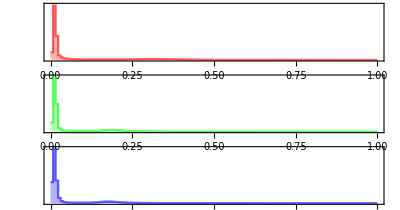

```mathematica
ImageHistogram[fig,Appearance->"Separated"]
```

```mathematica
marker = Dilation[Binarize[fig,0.6],DiskMatrix[9]]
```

-Graphics-

```mathematica
w = WatershedComponents[GradientFilter[marker,7],marker, Method-> "Rainfall"(*Method->"Basins"*)(*Method->{"MinimumSaliency",.0}*)(* Method-> "Rainfall"*)];
Colorize[w]
```

-Graphics-

```mathematica
measures[[All,2,2]]+10
```

{21.9416,19.7557,17.2691,19.4575,21.027,21.7265,22.1792,22.0742,21.027,21.7941,21.0414,21.2838,21.9816,21.1132,22.425,21.8076,20.8083,20.4945,22.5524,21.6447,21.312,23.6459,22.6535,20.7196,23.0009,22.603,23.0497,21.3401,21.1846,21.0558,22.2053,22.2573,20.7788,22.5904,21.5624,22.0213,21.7265,21.8614,20.94,21.2979,22.2573,23.0741,21.915,22.3221,21.2272,21.027,22.1792,20.0925,23.2314,21.5487,19.9656,22.1922,21.1846,22.3865,22.1137,22.4634,23.7041,22.9272,21.326,20.1867,19.6574,20.8083,21.326,20.6152,22.4378,23.1227,20.7047,22.8283,23.3988,22.4506,20.7047,22.0081,22.3865,22.3736,23.5052,23.0863,23.1953,23.9687,21.9816,21.9683,20.9109,23.4225,23.0984,22.6283,23.5992,19.9656,24.3841,23.7852,24.4283,22.6409,22.2703,19.6574,23.3988,23.0009,21.7129,22.603,22.0213,22.1005,24.8415,24.0255,21.41,25.7165,21.1988,23.3154,22.0478,20.4945,20.3725,23.1711,20.4031,20.6301,24.0935,19.6574,20.7196,20.4945,24.3841,24.0028}

```mathematica
(*b1=Binarize[Blur[fig,3]];
b=DeleteSmallComponents[b1,500];*)
marker = Dilation[Binarize[fig,0.6],DiskMatrix[9]]
(*w = WatershedComponents[GradientFilter[marker,7],marker, Method-> "Rainfall"];
Colorize[w]*)
umbrellas = SelectComponents[marker,"Count",50<#<2000 &];
measures = ComponentMeasurements[umbrellas, {"Centroid","EquivalentDiskRadius","Label"}];
measures[[All,2,2]]=measures[[All,2,2]]+15;
binaryDetections = Graphics[{LightGreen, {Green,Circle@@ # &/@(measures⟦All,2,1
;;2⟧)},MapThread[Text,{measures⟦All,2,3⟧,measures⟦All,2,1⟧}]}];
Show[fig,binaryDetections,ImageSize->Large]
Max[measures⟦All,2,3⟧]
```

-Graphics-

-Graphics-

116

```mathematica
b1=Binarize[Blur[fig,3]]
(*b1=Binarize[mfig]*)  (*mean blur was bad*)
b=DeleteSmallComponents[b1,500];
distT=DistanceTransform[b,Padding-> 0];
marker = MaxDetect[ImageAdjust[distT],0.02];
w = WatershedComponents[GradientFilter[b,3],marker, Method-> "Rainfall"];
Colorize[w]
```

-Graphics-

-Graphics-

```mathematica
umbrellas = SelectComponents[w,"Count",500<#<6000 &];
measures = ComponentMeasurements[umbrellas, {"Centroid","EquivalentDiskRadius","Label"}];
Show[fig,binaryDetections,Graphics[{White, Circle@@ # &/@(measures⟦All,2,1
;;2⟧),MapThread[Text,{measures⟦All,2,3⟧,measures⟦All,2,1⟧}]}],ImageSize->Large]
Max[measures⟦All,2,3⟧]
```

-Graphics-

164

```mathematica
Max[measures⟦All,2,3⟧]
```

164

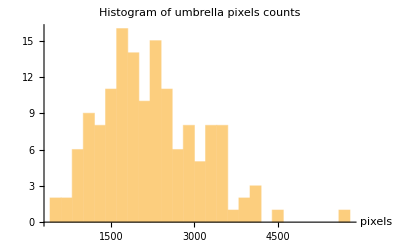

```mathematica
Histogram[ComponentMeasurements[umbrellas,"Count"]⟦All,2⟧,20,AxesLabel-> {"pixels"},PlotLabel-> "Histogram of umbrella pixels counts"]
```

```mathematica
smFig = ImageResize[fig,300];
DominantColors[smFig]
```

{-Graphics-}

```mathematica
noBack = ColorReplace[smFig,Black,0.05]
```

-Graphics-

```mathematica
DominantColors[RemoveAlphaChannel[noBack,White],10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DominantColors[fig]
```

$Aborted

```mathematica
res=DominantColors[fig,Automatic,{"CoverageImage","Color"}]
```

```mathematica
f2=Sharpen[Blur[fig,10],15]
b4=Binarize[Blur[f2,3]];
b5=DeleteSmallComponents[b4,500];
(*processing the blurred/sharpened image didn't improve result*)
```

```mathematica
b5
```

```mathematica
fig =Import[StringJoin[NotebookDirectory[],"KeyFrames/frameRel0000003.jpg"]];

smFig = ImageResize[fig,300];
b=Binarize[smFig];
distT=DistanceTransform[b,Padding-> 0];
marker = MaxDetect[ImageAdjust[distT],0.02];
w = WatershedComponents[GradientFilter[b,2],marker, Method-> "Rainfall"];
Colorize[w]

umbrellas = SelectComponents[w,"Count",10<#<150 &];
measures = ComponentMeasurements[umbrellas, {"Centroid","EquivalentDiskRadius","Label"}];
Show[smFig,Graphics[{White, Circle@@ # &/@(measures⟦All,2,1
;;2⟧),MapThread[Text,{measures⟦All,2,3⟧,measures⟦All,2,1⟧}]}],ImageSize->Large]
Max[measures⟦All,2,3⟧]
```

-Graphics-

-Graphics-

138

### How do I get the dominant color at a given location?

```mathematica
iDim = ImageDimensions[smFig];
sam = 200;
oneUmbrella=ImageTake[smFig,
Clip[Round[iDim⟦2⟧-measures⟦sam,2,1,2⟧+measures⟦sam,2,2⟧*.7*{-1,1}],{1,iDim⟦2⟧} ],
Clip[Round[measures⟦sam,2,1,1⟧+measures⟦sam,2,2⟧*.7*{-1,1}],{1,iDim⟦1⟧} ]]
colorsInImage =DominantColors[oneUmbrella,1]
```

Part::partw: Part 200 of {1 → {{1094.64, 1063.98}, 24.391, 1}, 2 → {{814.643, 1057.38}, 32.7619, 2}, 3 → {{947.1, 1052.82}, 34.8749, 3}, « 46 », 58 → {{156.924, 732.375}, 20.5135, 58}, « 50 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ImageTake::taker: Cannot take the specified rows of the image.

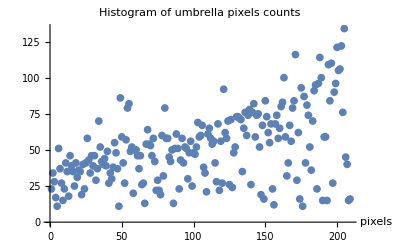

```mathematica
ListPlot[ComponentMeasurements[umbrellas,"Count"]⟦All,2⟧,AxesLabel-> {"pixels"},PlotLabel-> "Histogram of umbrella pixels counts"]
```

```mathematica
NotebookDirectory[]<>"KeyFrames/frameRel"<>IntegerString[5,7,4]<>".jpg"
```

/Users/ab55/Desktop/git/visionTracking/KeyFrames/frameRel0005.jpg

/Users/ab55/Desktop/git/visionTracking/KeyFrames/frameRel0000002.jpg

-Graphics-

### ProcessMany Images

```mathematica
frameData = Table[
filename = NotebookDirectory[]<>"KeyFrames/frameRel"<>IntegerString[i,10,7]<>".jpg";
fig =Import[filename];

smFig = ImageResize[fig,300];
b=Binarize[smFig];
distT=DistanceTransform[b,Padding-> 0];
marker = MaxDetect[ImageAdjust[distT],0.02];
w = WatershedComponents[GradientFilter[b,2],marker, Method-> "Rainfall"];
Colorize[w];
umbrellas = SelectComponents[w,"Count",8<#<150 &];
measures = ComponentMeasurements[umbrellas, {"Centroid","EquivalentDiskRadius","Label"}];
{Show[smFig,Graphics[{White, Circle@@ # &/@(measures⟦All,2,1
;;2⟧),MapThread[Text,{measures⟦All,2,3⟧,measures⟦All,2,1⟧}]}],ImageSize->Large],
Max[measures⟦All,2,3⟧]},
{i,1,9}]
```

{{-Graphics-,214},{-Graphics-,188},{-Graphics-,138},{-Graphics-,167},{-Graphics-,186},{-Graphics-,182},{-Graphics-,138},{-Graphics-,115},{-Graphics-,162}}

```mathematica
N[(200-15)/200]
```

0.925

```mathematica
N[Mean[frameData[[All,2]]]]
```

165.778

```mathematica
ImageCollage[frameData[[All,1]],Automatic,10000,ImagePadding->2,Background->White]
```

```mathematica
Grid[Transpose[{frameData[[All,1]]}]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"Processed1.pdf",frameData[[1,1]]]
```

/Users/ab55/Desktop/git/visionTracking/Processed1.pdf